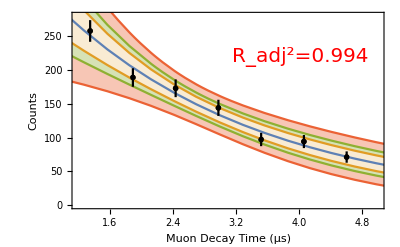

```mathematica
Needs["ErrorBarPlots`"]
data=Import[NotebookDirectory[]<>"Mathematica_format.txt","Table"];
errors = Table[√data[[i,2]],{i,1,Length[data]}];
errorbars = Table[ErrorBar[errors[[i]]],{i,1,Length[data]}];
ziperrorbardata = MapThread[List,{data,errorbars}];
weights = Table[1/errors[[i]]^2,{i,1,Length[data]}];
model = a ⅇ^(-t/τ);
nlm =NonlinearModelFit[data,model,{a,τ},t, Weights->weights];
sols = nlm["BestFitParameters"];
bestfit = model/.sols;
τuncertainty = Round[nlm["ParameterErrors"][[2]],0.01];
radjsquared = Round[nlm["AdjustedRSquared"],0.001];
{bands90[t_],bands95[t_],bands99[t_]} = Table[nlm["MeanPredictionBands", ConfidenceLevel->conf],{conf,{0.95,0.99,0.999}}];

marker = Graphics[{Black, Disk[]}];
legendstyle = Directive[FontFamily->"Arial",Black,FontSize->9];

plot1=ListPlot[data,PlotMarkers->{marker, 0.025}, PlotLegends->Placed[{"Data"},{Left, Bottom}], LabelStyle->legendstyle];
plot2 = Plot[{nlm[t],bands90[t],bands95[t],bands99[t]},{t,1,15},Filling->{2->{1},3->{2},4->{3}},PlotLegends->Placed[{"Best Fit τ="<>ToString[Round[(τ/.sols),0.01]]<>"±"<>ToString[τuncertainty]<>" μs","90% Confidence Level","95% Confidence Level","99% Confidence Level"},{Left,Bottom}],LabelStyle->legendstyle, PlotRange->{{1.0,5},{0,300}}];
plot3 = ErrorListPlot[ziperrorbardata, PlotMarkers->{marker,0.025}, PlotStyle->Black];
text = Text[Style["R_adj^2="<>ToString[radjsquared],Red,20],{3.15,220},{-1,0}];
textgfx = Graphics[text];
finalplot=Show[plot1,plot2,plot3,textgfx,FrameLabel->{{"Counts",""},{"Muon Decay Time (μs)",""}},Frame->True, PlotRange->{{1.2,5},{0,280}}]
Export[NotebookDirectory[]<>"MuonLifetimePlot.svg",finalplot, "SVG"];
Export[NotebookDirectory[]<>"MuonLifetimePlot.png",finalplot, "PNG"];
```